```mathematica
hc2=0.389379338;alfa=7.297352568 10^(-3);
```

```mathematica
rho=0.145;sigmaTOT=98.6;B=19.89;
```

```mathematica
hc=Sqrt[hc2];
```

```mathematica
Gt=(1+Abs[t]/0.71)^(-2);
```

```mathematica
phidet=Log[0.08/Abs[t]]-0.577;
```

```mathematica
dfn=sigmaTOT^2 (rho^2+1)*Exp[-B Abs[t]]/(16*Pi*hc2);
```

```mathematica
dinter=-alfa (rho+alfa phidet)sigmaTOT Gt^2/(Abs[t])Exp[-B Abs[t]/2];
```

```mathematica
dsc=4Pi hc2 alfa*alfa Gt^4/(Abs[t]^2);
```

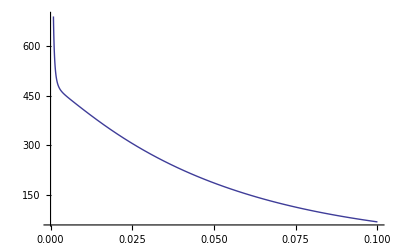

```mathematica
Plot[dfn+dinter+dsc,{t,0,0.1}]
```

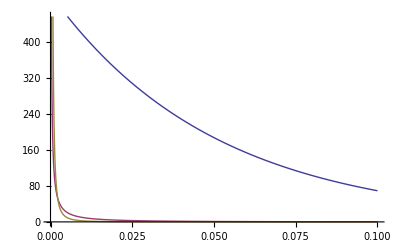

```mathematica
Plot[{dfn,dinter,dsc},{t,10^(-5),0.1}]
```